# From the 1D profile to amplitude distribution

Let’s consider a  linear machine a
nd a matched density distribution ρ(x, px) in the the 2D normalized phase space {x, px}. 
Starting from the x-projection of ρ, ρ_x=∫ρⅆxp, we aim to determine the corresponding amplitude distribution, ρ_r(r=√(x^2+px^2)), and the action distribution, ρ_J(J=r^2/2=(x^2+px^2)/2).

ρ_r is distributed as the inverse Abel transform of ρ_x after MULTIPLYING it by 2π r: ρ_r = 2 π r 

ρ_J is distributed as the inverse Abel transform of ρ_x, after replacing r->√(2J) and MULTIPLYING it by 2π.
Note that ρ, ρ_x, ρ_r and ρ_J are already normalized such that their integral is 1.

```mathematica
$Assumptions={x∈Reals, 1<q<3, β >0, r>0 };
InverseAbelTransform[A_,r_]:=-(1/Pi) Integrate[Derivative[1][A][x]/Sqrt[x^2-r^2],{x,r,Infinity},Assumptions->r>=0]
AbelTransform[f_,x_]:=2 Integrate[r f[r]/Sqrt[r^2-x^2],{r,x,Infinity}]
```

```mathematica
exampleFunction[x_]:=1/(√(2 π))Exp[- x^2/2]
```

(ⅇ^(-r^2/2))/(2 π)

Inverse Abel Transform of 1/(√(2 π))Exp[- x^2/2]: (ⅇ^(-r^2/2))/(2 π)

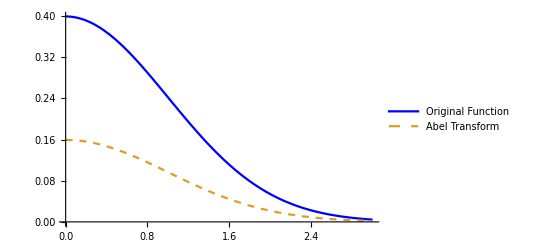

```mathematica
inverseAbelGaussian=Simplify[InverseAbelTransform[exampleFunction,r]]
Print["Inverse Abel Transform of 1/(√(2 π))Exp[- x^2/2]: ",inverseAbelGaussian]
Plot[{exampleFunction[r],inverseAbelGaussian},{r,0,3},PlotLegends->{"Original Function","Abel Transform"},PlotStyle->{Blue,Dashed}]
```

```mathematica
exampleFunction[r_]:=(ⅇ^(-r^2/2))/(2 π)
abelGaussian=Simplify[AbelTransform[exampleFunction,x]]
```

ConditionalExpression[(ⅇ^(-x^2/2))/(√(2 π)), x>0]

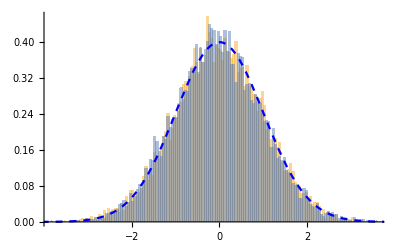

```mathematica
xValues =RandomVariate[NormalDistribution[0,1],10000];
pxValues =RandomVariate[NormalDistribution[0,1],10000];
U1 = RandomVariate[UniformDistribution[],10000];
U2 = RandomVariate[UniformDistribution[],10000];

xValuesBM=√(-2Log[U1])Cos[2 Pi U2];
pxValuesBM = √(-2Log[U1])Sin[2 Pi U2];

Show[Histogram[{xValues,xValuesBM},100,"PDF"],
Plot[1/(√(2 π))Exp[- x^2/2], {x,-5,5},PlotStyle->{Blue,Dashed}]
]
```

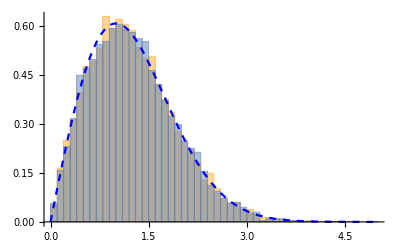

```mathematica
Show[
Histogram[{√(xValues^2+pxValues^2),√(xValuesBM^2+pxValuesBM^2)},50,"PDF"],

Plot[2 *Pi*r*inverseAbelGaussian,{r,0,5},PlotStyle->{Blue,Dashed}]
]
```

```mathematica
Simplify[Integrate[Simplify[2 *Pi*r*inverseAbelGaussian,  Assumptions->r>0 ], {r, rr, +∞}]]
```

ⅇ^(-rr^2/2)

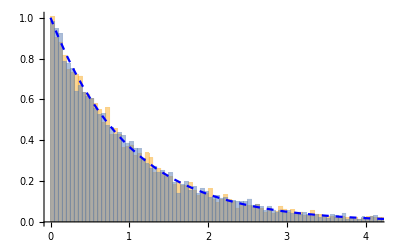

```mathematica
Show[Histogram[{(xValues^2+pxValues^2)/2, (xValuesBM^2+pxValuesBM^2)/2},200,"PDF"], Plot[2 *Pi*inverseAbelGaussian/.{r->√(2J)},{J,0,5},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Simplify[Integrate[Simplify[2 *Pi*inverseAbelGaussian/.{r->√(2J)},  Assumptions->J>0 ], {J, JJ, +∞}]]
```

ⅇ^-JJ

## From Gaussian to qGaussian

```mathematica
exampleFunction[x_]:= PDF[TsallisQGaussianDistribution[0,β,q],x]
inverseAbelGaussian=Simplify[InverseAbelTransform[exampleFunction,r]]
```

-(2^((5-3 q)/(2 (-1+q))) (-3+q) (r/β)^((1+q)/(1-q)) (-1+q+(2 β^2)/r^2)^((1+q)/(2-2 q)))/(π β^2)

```mathematica
inverseAbelGaussian/. {β->1}
```

-(2^((5-3 q)/(2 (-1+q))) (-3+q) (-1+q+2/r^2)^((1+q)/(2-2 q)) r^((1+q)/(1-q)))/π

```mathematica
f[x_]= -(2^((5-3 q)/(2 (-1+q))) (-3+q) (-1+q+2/x^2)^((1+q)/(2-2 q)) x^((1+q)/(1-q)))/π
```

-(2^((5-3 q)/(2 (-1+q))) (-3+q) (-1+q+2/x^2)^((1+q)/(2-2 q)) x^((1+q)/(1-q)))/π

```mathematica
InverseFunction[f][y]
```

Inverse[f][y]

```mathematica
Limit[inverseAbelGaussian/. {β->1}, q->1, Direction->1]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(ⅇ^(-r^2/2))/(2 π)

```mathematica
StandardDeviation[TsallisQGaussianDistribution[0,√((5-3q)/2),q]]
Median[TsallisQGaussianDistribution[0,√((5-3q)/2),q]]
```

Piecewise[{{1, q<5/3}, {∞, 5/3≤q<2}, {Indeterminate, True}}]

0

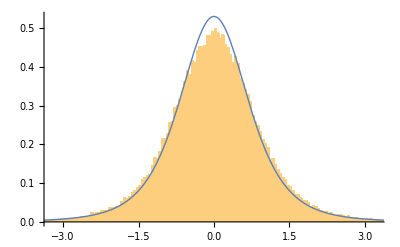

```mathematica
(*Define ln_q(x) based on the conditions provided*)
QLog[x_,q_]:=(x^(1-q)-1)/(1-q)

U1 = RandomVariate[UniformDistribution[],100000];
U2 = RandomVariate[UniformDistribution[],100000];

xValuesBM=√(-2QLog[U1,1.4])Cos[2 Pi U2];
pxValuesBM = √(-2QLog[U1,1.4])Sin[2 Pi U2];
Show[Histogram[xValuesBM/StandardDeviation[xValuesBM],600,"PDF"],
Plot[PDF[TsallisQGaussianDistribution[0,√((5-3 1.4)/2),1.4],x]//Evaluate,{x,-4,4},PlotStyle->Thick]]
```

```mathematica
0,√((5-3q)/2),q
```

```mathematica
StandardDeviation[xValuesBM/StandardDeviation[xValuesBM]]
```

1.

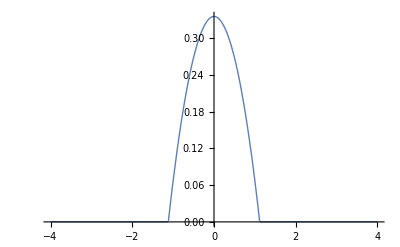

```mathematica
Plot[PDF[TsaallisQGaussianDistribution[0,√((5-3 0)/2),0],x*2]//Evaluate,{x,-4,4},PlotStyle->Thick]
```

```mathematica
myq=1.4;
On[Assert]
Assert[myq<=5/3];
PDF[TsallisQGaussianDistribution[0,β, myq], x]
```

0.33541/((1+(0.2 x^2)/β^2)^2.5 β)

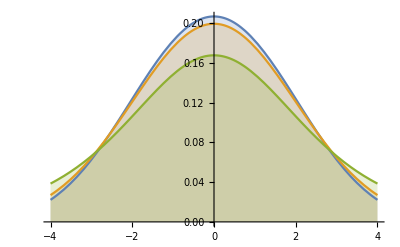

```mathematica
Plot[Table[PDF[TsallisQGaussianDistribution[0,2,q],x],{q,{0.9,1,1.4}}]//Evaluate,{x,-4,4},Filling->Axis]
```

```mathematica
Limit[-((βq^(3/2) (q-3) Sqrt[q-1] rx)/(2 π))*((1/(βq (q-1) rx^2)+1)^((q+1)/(2-2 q)))*(βq (q-1) rx^2)^((q)/(1-q)),q->1, Direction->"FromAbove",Assumptions->{rx>0}]
```

ConditionalExpression[(ⅇ^(-rx^2 βq) βq)/π, βq>0&&Log[1/βq]+Log[βq]==0]

```mathematica
Simplify[Integrate[Simplify[-((βq^(3/2) (q-3) Sqrt[q-1] rx)/(2 π))*((1/(βq (q-1) rx^2)+1)^((q+1)/(2-2 q)))*(βq (q-1) rx^2)^((q)/(1-q)),  Assumptions->rx>0 ], {rx, rr, +∞}]]
```

ConditionalExpression[-((-3+q) √(-1+q) √βq ((-1+q) rr^2 βq)^(1/(1-q)) Hypergeometric2F1[1/2+1/(-1+q),1/(-1+q),q/(-1+q),1/(rr^2 βq-q rr^2 βq)])/(4 π), Re[(-3+q)/(-1+q)]<1&&Re[rr]>0&&Im[rr]==0]

## Non - factorization

```mathematica
myN= 100000;
jx=RandomVariate[ExponentialDistribution[1],myN];
jy = RandomVariate[ExponentialDistribution[1],myN];
jy =jx
thetax=2*Pi*RandomReal[{0,1},myN];
thetay = 2*Pi*RandomReal[{0,1},myN];
x = Sqrt[jx]*Cos[thetax];
px = Sqrt[jx]*Sin[thetax];
y = Sqrt[jy]*Cos[thetay];
py = Sqrt[jy]*Sin[thetay];
```

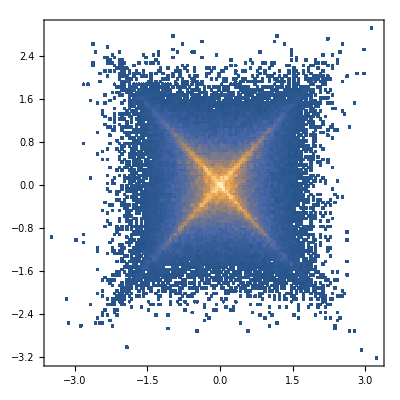

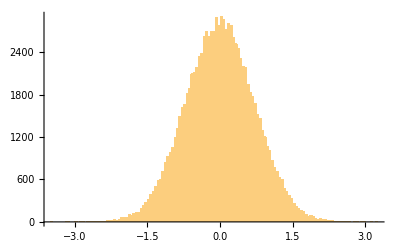

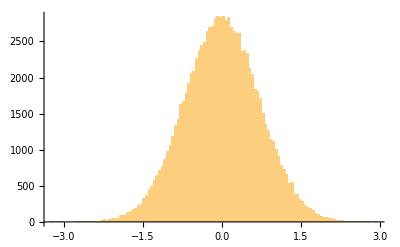

```mathematica
DensityHistogram[Transpose[{x,y}],100]
Histogram[x,100]
Histogram[y,100]
```

```mathematica
TransformedDistribution[ u+v ,{u\[Distributed]TsallisQGaussianDistribution[0,1,1],v\[Distributed]TsallisQGaussianDistribution[0,1,1]}]
```

TransformedDistribution[x1+x2,{x1\[Distributed]TsallisQGaussianDistribution[0,1,1],x2\[Distributed]TsallisQGaussianDistribution[0,1,1]}]

```mathematica
x1\[Distributed]NormalDistribution[0,1]
```

x1\[Distributed]NormalDistribution[0,1]

```mathematica
TransformedDistribution[u+v,{u\[Distributed]NormalDistribution[μ,σ], v\[Distributed]NormalDistribution[μ,σ]}]
```

NormalDistribution[2 μ,√2 Abs[σ]]

```mathematica
TransformedDistribution[-Cos[θ]u-Sin[θ]v,{u\[Distributed]NormalDistribution[0,σ], v\[Distributed]NormalDistribution[0,σ]}]
```

NormalDistribution[0,√(σ^2 Cos[θ]^2+σ^2 Sin[θ]^2)]

```mathematica
TransformedDistribution[-Cos[θ]u-Sin[θ]v,{u\[Distributed]StableDistribution[2], v\[Distributed]StableDistribution[2]}]
```

TransformedDistribution[-x1 Cos[θ]-x2 Sin[θ],{x1\[Distributed]StableDistribution[1,2,0,0,1],x2\[Distributed]StableDistribution[1,2,0,0,1]}]

```mathematica
TsallisQExp[x_,q_]:=Piecewise[{{Exp[x],q==1},(*Standard exponential for q=1*){(1+(1-q) x)^(1/(1-q)),1+(1-q) x>0},{0,True}  (*Define 0 for invalid regions*)}]


rho[x_,y_,q_, β_]:= ((3-q) β)/(2 π)TsallisQExp[-((1+q)β)/2(x^2+y^2),(3 q-1)/(1+q)]
rhoPolar[r_,q_, β_]:= ((3-q) β)/(2 π)TsallisQExp[-((1+q)β)/2 r^2,(3 q-1)/(1+q)]

Integrate[rho[x,y,q, 1],{x, -∞, +∞},{y, -∞, +∞}]
```

1

```mathematica
N[(-3 Gamma[3/2+1/(1-q)] Gamma[-1/2+1/(-1+q)]-π q Sec[π/(-1+q)])/((-3+q) Gamma[3/2+1/(1-q)] Gamma[-1/2+1/(-1+q)])/.q->.99]-1
```

```mathematica
Assuming[1<=q<5/3,Integrate[rho[x,y,q,1/(5-3 q)],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]]
```

Piecewise[{{1, 1/(1+q)-(3 q)/(1+q)==-1}, {-((-3+q) Gamma[1/(-1+q)] (2 π Gamma[1/(-1+q)] Hypergeometric2F1[-1/2,1/2,(-2+q)/(-1+q),1]-Gamma[1/(1-q)] Gamma[-(-3+q)/(2 (-1+q))] Gamma[(1+q)/(2 (-1+q))] Hypergeometric2F1[-1/2+1/(-1+q),1/2+1/(-1+q),q/(-1+q),1]))/(4 π (-1+q) Gamma[(1+q)/(2 (-1+q))]^2), True}}]

```mathematica
N[-((-3+q) Gamma[1/(-1+q)] (2 π Gamma[1/(-1+q)] Hypergeometric2F1[-1/2,1/2,(-2+q)/(-1+q),1]-Gamma[1/(1-q)] Gamma[-(-3+q)/(2 (-1+q))] Gamma[(1+q)/(2 (-1+q))] Hypergeometric2F1[-1/2+1/(-1+q),1/2+1/(-1+q),q/(-1+q),1]))/(4 π (-1+q) Gamma[(1+q)/(2 (-1+q))]^2)/.q->1.4]
```

Power::infy: Infinite expression 1/0.^1.5 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

```mathematica
Integrate[rho[x,y,1.65,1/(5-3 *1.65)],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1.

Integrate::pwrl: Unable to prove that integration limits {-a,a} are real. Adding assumptions may help.

```mathematica
Assuming[1<=a<=6,Integrate[rho[x,y,1.1,1/(5-3 *1.1)],{x,-a,a},{y,-a,a}]]
```

```mathematica
((3-q) β)/(2 π)TsallisQExp[-((1+q)β)/2(x^2+y^2),(3 q-1)/(1+q)]/.β->1/(5-3 q)
```

((3-q) (Piecewise[{{ⅇ^(-((1+q) (x^2+y^2))/(2 (5-3 q))), (-1+3 q)/(1+q)==1}, {(1-((1+q) (1-(-1+3 q)/(1+q)) (x^2+y^2))/(2 (5-3 q)))^(1/(1-(-1+3 q)/(1+q))), 1-((1+q) (1-(-1+3 q)/(1+q)) (x^2+y^2))/(2 (5-3 q))>0}, {0, True}}]))/(2 π (5-3 q))

```mathematica
Integrate[rhoPolar[r,2., 4]r,{r, 0, +∞},{theta, 0, 2π}]
```

1.

```mathematica
N[(-(2^((5-3 q)/(2 (-1+q))) (-3+q) (r/β)^((1+q)/(1-q)) (-1+q+(2 β^2)/r^2)^((1+q)/(2-2 q)))/(π β^2)-rhoPolar[r,q, β])/.{q->1.2,β->1.,r->1}]
```

-0.020297

```mathematica
Cq[q_]:=Piecewise[{{2 Sqrt[Pi] Gamma[1/(1-q)]/((3-q) Sqrt[1-q] Gamma[(3-q)/(2 (1-q))]),q<1},{Sqrt[Pi],q==1},{Sqrt[Pi] Gamma[(3-q)/(2 (q-1))]/(Sqrt[q-1] Gamma[1/(q-1)]),1<q<3}}]

(*Define the q-Gaussian function*)
qGaussian[x_,q_,beta_]:=(Sqrt[beta]/Cq[q])*TsallisQExp[-beta x^2,q]
```

```mathematica
Manipulate[Plot[qGaussian[x,q,1],{x,-3,3},PlotRange->{0,1.5},AxesLabel->{"x","f_q(x)"},PlotStyle->{Thick,Blue}],{{q,1,"q"},-1,2.9,0.1}]
```

Check that the approach of Elleanor is similar to the one of the Box-Muller

```mathematica
exampleFunction[x_]:=qGaussian[x,q,beta]
```

```mathematica
inverseAbelGaussian=Simplify[InverseAbelTransform[exampleFunction,r]]
```

-Integrate[(√beta Gamma[1/(-1+q)] (Piecewise[{{-2 beta x (1+beta (-1+q) x^2)^(q/(1-q)), beta (-1+q) x^2>-1}, {0, True}}]))/(√π √((-r^2+x^2)/(-1+q)) Gamma[-(-3+q)/(2 (-1+q))]),{x,r,∞},Assumptions→True]/π

```mathematica
inverseAbelGaussian
```

-Integrate[(√beta Gamma[1/(-1+q)] (Piecewise[{{-2 beta x (1+beta (-1+q) x^2)^(q/(1-q)), beta (-1+q) x^2>-1}, {0, True}}]))/(√π √((-r^2+x^2)/(-1+q)) Gamma[-(-3+q)/(2 (-1+q))]),{x,r,∞},Assumptions→True]/π

```mathematica
f2D[r_,q_,β_]:=-(β^(3/2) (q-3) Sqrt[q-1] r)/(2 π)*((1/(β (q-1) r^2)+1)^((q+1)/(2-2 q))*(β (q-1) r^2)^(q/(1-q)))
```

```mathematica
FullSimplify[f2D[r,q,β]-rhoPolar[r,q, β]]/.{r->.2, q->1.5, β->2.}
```

-5.30092×10^-17

## Some simplification

#### Triple Abel

```mathematica
FullSimplify[(3-q)β/(2π)CC[(3q-1)/(1+q)]/√((1+q)β/2)FullSimplify[  (3-q)β/(2π) /. { q->(3q-1)/(1+q), β-> (1+q)β/2}]]
```

-((-3+q) β^2 CC[3-4/(1+q)])/(√2 π^2 √((1+q) β))

```mathematica
FullSimplify[(3q-1)/(1+q) /. q->(3q-1)/(1+q)]
```

2-1/q

```mathematica
FullSimplify[(1+q)β/2 /.{ q->(3q-1)/(1+q), β-> (1+q)β/2}]
```

q β

#### 4th Abel

```mathematica
Simplify[-((-3+q) β^2 CC[3-4/(1+q)])/(√2 π^2 √((1+q) β))CC[2-1/q]/√(q β) FullSimplify[(3-q)β/(2π) /. { q->(2-1/q), β-> q β}]]
```

-((-3+q) (1+q) β^2 CC[2-1/q] CC[3-4/(1+q)])/(2 √2 π^3 √(q (1+q)))

```mathematica
FullSimplify[(2-1/q)/. q->(2-1/q)]
```

(2-3 q)/(1-2 q)

```mathematica
FullSimplify[β q /. { q->(2-1/q), β-> qβ}]
```

```mathematica
(2-1/q) qβ
```

```mathematica
myExp[x_,q_] :=(1+(1-q) x)^(1/(1-q)) 
myExp2[x_,q_]:=Piecewise[{{(1+(1-q) x)^(1/(1-q)),1+(1-q) x<0},{0,True}}]
```

```mathematica
myExp[0,2]
```

1

```mathematica
Integrate[ (β  (3-q))/(2 π) myExp[- (β  (1+q))/2(x^2+px^2),(3 q-1)/(1+q)], {px,√(x0^2-x^2),-√(x0^2-x^2)}]
```

ConditionalExpression[-((-3+q) β (-((1+(-1+q) x0^2 β)^(1/2+1/(1-q)) ((1+(-1+q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),-1/2,((-1+q) (x^2-x0^2) β)/(1+(-1+q) x^2 β)]+(-1+(-5+3 q) x^2 β+(6-4 q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),1/2,((-1+q) (x^2-x0^2) β)/(1+(-1+q) x^2 β)]))/((-3+q) √(-x^2+x0^2) β (1+(-1+q) x^2 β))-(√(-x^2+x0^2) (1+(-1+q) x0^2 β)^(1/2+1/(1-q)) Hypergeometric2F1[1,(-2+q)/(-1+q),3/2,((-1+q) (x^2-x0^2) β)/(1+(-1+q) x^2 β)])/(1+(-1+q) x^2 β)))/(2 π), ]

```mathematica
FullSimplify[ConditionalExpression[-((-3+q) β (-((1+(-1+q) x0^2 β)^(1/2+1/(1-q)) ((1+(-1+q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),-1/2,((-1+q) (x^2-x0^2) β)/(1+(-1+q) x^2 β)]+(-1+(-5+3 q) x^2 β+(6-4 q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),1/2,((-1+q) (x^2-x0^2) β)/(1+(-1+q) x^2 β)]))/((-3+q) √(-x^2+x0^2) β (1+(-1+q) x^2 β))-(√(-x^2+x0^2) (1+(-1+q) x0^2 β)^(1/2+1/(1-q)) Hypergeometric2F1[1,(-2+q)/(-1+q),3/2,((-1+q) (x^2-x0^2) β)/(1+(-1+q) x^2 β)])/(1+(-1+q) x^2 β)))/(2 π), ]]
```

ConditionalExpression[-1/(2 √(-x^2+x0^2) (π+π (-1+q) x^2 β))(-3+q) β (1+(-1+q) x0^2 β)^(1/2+1/(1-q)) (-((1+(-1+q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),-1/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)]+(-1+(-5+3 q) x^2 β+(6-4 q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),1/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)])/((-3+q) β)+(x-x0) (x+x0) Hypergeometric2F1[1,(-2+q)/(-1+q),3/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)]), ]

```mathematica
2 Integrate[ (β  (3-q))/(2 π) myExp[- (β  (1+q))/2(x^2+px^2),(3 q-1)/(1+q)], {px,√(x0^2-x^2),0}]
```

ConditionalExpression[((1+(-1+q) x0^2 β)^(1/2+1/(1-q)) ((1+(-1+q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),-1/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)]+(-1+(-5+3 q) x^2 β+(6-4 q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),1/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)]))/(π √(-x^2+x0^2) (1+(-1+q) x^2 β)), ]

```mathematica
Hypergeometric2F1
```

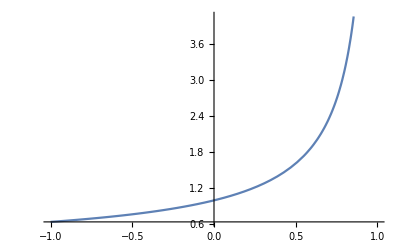

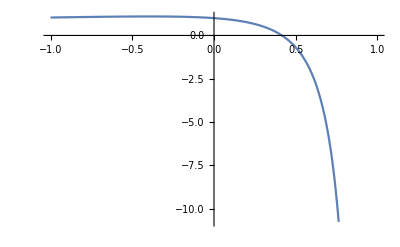

```mathematica
Plot[Hypergeometric2F1[1,1/3,1/2,x],{x,-1,1}]
Plot[Hypergeometric2F1[1,1/3,1/2,x],{x,-1,1}/Hypergeometric2F1[1,1/3,-1/2,x],{x,-1,1}]
```

```mathematica
Plot[Hypergeometric2F1[1,1/3,1/2,x]-Hypergeometric2F1[1,1/3,-1/2,x],{x,-1,1}]
```

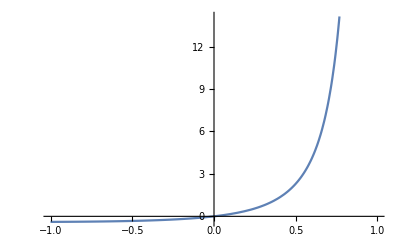

-Graphics-

```mathematica
Integrate[(((1+(-1+q) x0^2 β)^(1/2+1/(1-q)) ((1+(-1+q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),-1/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)]+(-1+(-5+3 q) x^2 β+(6-4 q) x0^2 β) Hypergeometric2F1[1,(-2+q)/(-1+q),1/2,((-1+q) (x-x0) (x+x0) β)/(1+(-1+q) x^2 β)]))/(π √(-x^2+x0^2) (1+(-1+q) x^2 β)))^2, {x,0, x0}]
```

$Aborted

```mathematica
Integrate[  myExp[- β x^2,q]^2, {x,0, +∞}]/((√π Gamma[-1/2+1/(-1+q)])/(2 √((-1+q) β) Gamma[1/(-1+q)]))^2
```

ConditionalExpression[(2 (-1+q) β Gamma[-1/2+2/(-1+q)] Gamma[1/(-1+q)]^2)/(√π √((-1+q) β) Gamma[-1/2+1/(-1+q)]^2 Gamma[2/(-1+q)]), ]

```mathematica
FullSimplify[(2 (-1+q) β Gamma[-1/2+2/(-1+q)] Gamma[1/(-1+q)]^2)/(√π √((-1+q) β) Gamma[-1/2+1/(-1+q)]^2 Gamma[2/(-1+q)])]
```

(2 √((-1+q) β) Gamma[-1/2+2/(-1+q)] Gamma[1/(-1+q)]^2)/(√π Gamma[-1/2+1/(-1+q)]^2 Gamma[2/(-1+q)])

```mathematica
Integrate[  ((√β)/Cq myExp[- β x^2,q])^2, {x,0, +∞}, A]
```

ConditionalExpression[(√π β Gamma[-1/2+2/(-1+q)])/(2 Cq^2 √((-1+q) β) Gamma[2/(-1+q)]), ]

```mathematica
Simplify[(√π β Gamma[-1/2+2/(-1+q)])/(2 Cq^2 √((-1+q) β) Gamma[2/(-1+q)]), {β>1, q>1}]
```

(√π β Gamma[-1/2+2/(-1+q)])/(2 Cq^2 √((-1+q) β) Gamma[2/(-1+q)])

```mathematica
Assuming[{q<1,β>0}, Integrate[  ((√β)/Cq myExp2[- β x^2,q])^2, {x,0, +∞}]]
```

(√π β Gamma[(-3+q)/(-1+q)])/(2 Cq^2 √(-((-1+q) β)) Gamma[3/2-2/(-1+q)])

```mathematica
Assuming[{1<q<3,β>0}, Integrate[  ((√β)/Cq myExp2[- β x^2,q])^2, {x,0, +∞}]]
```

(√π β Gamma[-1/2+2/(-1+q)])/(2 Cq^2 √((-1+q) β) Gamma[2/(-1+q)])

```mathematica
Assuming[{q=1,β>0}, Integrate[  ((√β)/Cq myExp2[- β x^2,q])^2, {x,0, +∞}]]
```

$Assumptions::bass: 1 is not a well-formed assumption.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1^ComplexInfinity encountered.

Integrate::bass: 1 is not a well-formed assumption.

Integrate::idiv: Integral of Indeterminate does not converge on {0,∞}.

∫_0^∞ Indeterminateⅆx

```mathematica
Plot[Evaluate[myExp2[x_, 2]], {x, -4, 0}]
```

-Graphics-

```mathematica
Max[myExp[10, 5/3.],0]
```

Max::nord: Invalid comparison with 1.18068×10^-16+0.0741325 ⅈ attempted.

```mathematica
2.^-2.
```

0.25

```mathematica
myExp[x_,q_] :=Max[(1+(1-q) x),0]^(1/(1-q))
```

```mathematica
Assuming[{1<q<3,β>0}, Integrate[  ((√β)/Cq myExp[- β x^2,q])^2, {x,-∞, +∞}]]
```

(√π β Gamma[-1/2+2/(-1+q)])/(Cq^2 √((-1+q) β) Gamma[2/(-1+q)])

```mathematica
Assuming[{0<q<1,β>0}, Integrate[  ((√β)/Cq myExp[- β x^2,q])^2, {x,-∞, +∞}]]
```

(√π β Gamma[(-3+q)/(-1+q)])/(Cq^2 √(-((-1+q) β)) Gamma[3/2-2/(-1+q)])